```mathematica
Mac[q_]:=Binomial[420,q]*Binomial[180,100-q];
```

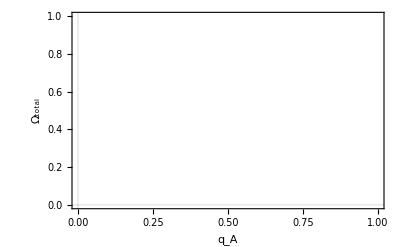

```mathematica
Plot[Mac[q],{q,0,100},PlotTheme->"Scientific",FrameLabel->{"q_A","Ω_total"},PlotStyle->Black,PlotRange->All]
```

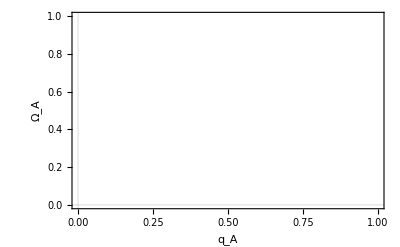

```mathematica
Plot[Binomial[420,q],{q,0,100},PlotTheme->"Scientific",FrameLabel->{"q_A","Ω_A"},PlotStyle->Black,PlotRange->All]
```

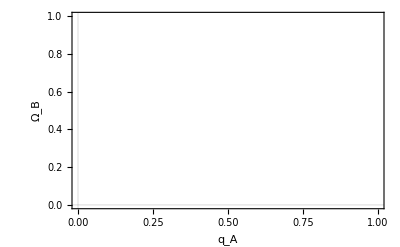

```mathematica
Plot[Binomial[180,100-q],{q,0,100},PlotTheme->"Scientific",FrameLabel->{"q_A","Ω_B"},PlotStyle->Black,PlotRange->All]
```

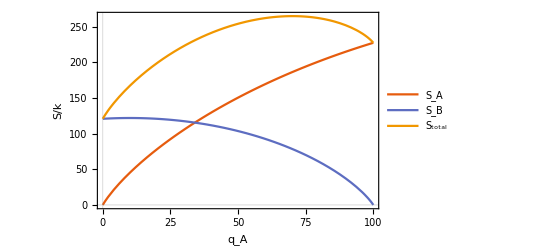

```mathematica
Plot[{Log[Binomial[420,q]],Log[Binomial[180,100-q]],Log[Binomial[420,q]*Binomial[180,100-q]]},{q,0,100},PlotTheme->"Scientific",FrameLabel->{"q_A","S/k"},PlotRange->All,PlotLegends->{"S_A","S_B","S_total"}]
```

```mathematica
Reverse@{Table[Log[Binomial[420,q]*Binomial[180,100-q]],{q,0,100,1}]//Max,Position[Table[Log[Binomial[420,q]*Binomial[180,100-q]],{q,0,100,1}],Table[Log[Binomial[420,q]*Binomial[180,100-q]],{q,0,100,1}]//Max][[1]][[1]]-1}
```

{70,Log[10564744627406371429067745866287013030933963751153995491215837889479996121507563551432088763588138167004023641495040]}

```mathematica
Max@Table[Log[Binomial[420,q]*Binomial[180,100-q]],{q,0,100,1}]
```

Log[10564744627406371429067745866287013030933963751153995491215837889479996121507563551432088763588138167004023641495040]

```mathematica
Plot[Mac[q]//N,{q,0,100},PlotRange->All]
```

-Graphics-

```mathematica
Mac[100]
```

1.33473×10^249

```mathematica
Binomial[q+420-1,q]*Binomial[q+180-1,q]
```

Binomial[179+q,q] Binomial[419+q,q]

```mathematica
DiscretePlot[Binomial[179+q,q] Binomial[419+q,q],{q,1,100}]
```

-Graphics-

```mathematica
Binomial[q+180-1,q]
```

575084207171625809589141484530485489449438547005302369805865402217095367859080